```mathematica
Clear["Global`*"];
```

```mathematica
data0T = Import["C:\\Users\\Jarvis\\Desktop\\X_TT0","Data"]
```

{{1.20312,0.943974},{1.3625,0.92278},{1.52187,0.889781},{1.68125,0.816574},{1.84062,0.680751},{2,0.51271},{2.15938,0.34707},{2.31875,0.217586},{2.47813,0.104006},{2.6375,0.0189738},{2.79688,0.00779484}}

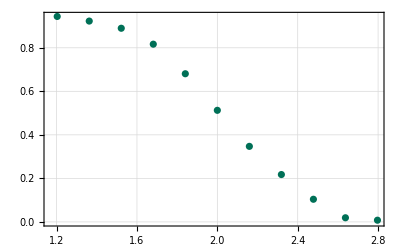

```mathematica
ListPlot[data0T,PlotTheme-> "Detailed", PlotStyle-> RGBColor[0.,0.44,0.34]]
```

```mathematica
modeldata0=(w+f*Erf[(x+q)/(√d)]);
```

```mathematica
fit=FindFit[data0T,modeldata0,{{w,0.4},{f,-0.345},{q,-2.1},{d,0.01}},{x}];
modelfundata0=Function[{x},Evaluate[modeldata0/.fit]];
```

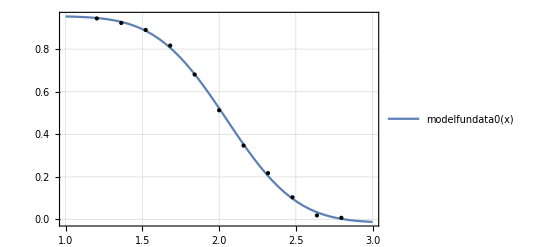

```mathematica
Plot[modelfundata0[x],{x,1,3},PlotTheme->"Detailed", Epilog->Map[Point,data0T]]
```

```mathematica
modeldata0/.fit
```

0.469841-0.485215 Erf[1.96654 (-2.04894+x)]

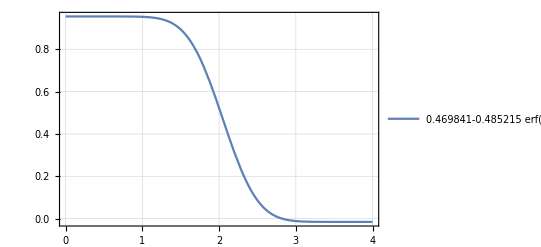

```mathematica
Plot[0.4698411076406618-0.4852153015261559 Erf[1.966544971940981 (-2.0489415062267593+x)],{x,0,4},PlotTheme->"Detailed"]
```

```mathematica
C0T[x_]:=0.4698411076406618-0.4852153015261559 Erf[1.966544971940981 (-2.0489415062267593+x)];
C0T[0]
```

0.955056

```mathematica
dCT0=D[T1[x,y],x]/.x->0;
dCTl=D[T1[x,y],x]/.x->4;
```

```mathematica
pdeModel[a0_?NumberQ,a1_?NumberQ,a2_?NumberQ]:=NDSolveValue[{D[T1[x,y],y]==D[(a0+a1*T1[x,y]+a2*(T1[x,y]^2))*D[T1[x,y],x],x],T1[x,0]==C0T[x],dCT0==0,dCTl==0},T1,{x,0,4},{y,0,1},Method->{"MethodOfLines","SpatialDiscretization"-> {"TensorProductGrid",MaxPoints-> 1000}}];
```

ifun = pdeModel[1.5227, 0.4014, 0.515]

```mathematica
ifun=pdeModel[(69/49),0.106531,0.120408]
```

InterpolatingFunction[…]

```mathematica
N1=Plot3D[ifun[x,y],{x,1,3},{y,0,1}]
```

-Graphics3D-

```mathematica
TT=Import["C:\\Users\\Jarvis\\Desktop\\TT","Data"];
```

```mathematica
N2=ListPointPlot3D[TT,PlotTheme->"Detailed",LabelStyle->Directive[Black, Medium],PlotStyle->{AbsolutePointSize[4],RGBColor[0.74,1.,0.]}]
```

-Graphics3D-

```mathematica
Show[N1,N2]
```

-Graphics3D-

```mathematica
ifun[1,0]
```

0.953343

```mathematica
TTt=Import["C:\\Users\\Jarvis\\Desktop\\TT","Data"];
```

```mathematica
Dimensions[TTt]
```

{440,3}

```mathematica
frac=TTt[[All,3]];
```

```mathematica
int=TTt[[All,2]];
```

```mathematica
pos=TTt[[All,1]];
```

```mathematica
sol[a0_,a1_,a2_]:=Norm[frac-pdeModel[a0,a1,a2][pos,int]]^2;
```

```mathematica
Residuals=Table[{{a,b,c},sol[a,b,c]},{a,1.4,2.1,(1.8-1.2)/59},{b,0.3,1.5,(0.7-0.1)/59},{c,0.3,0.8,(0.1-0.6)/59}];
```

```mathematica
Dimensions[Residuals]
```

{}

```mathematica
Min[Residuals[[All,All,All,2]]]
```

0.064473

```mathematica
Max[Residuals[[All,All,2]]]
```

41.3859

```mathematica
Position[Residuals,Min[Residuals[[All,All,2]]]]
```

{{11,23,2,2}}

```mathematica
Residuals[[11,23,2,All]]
```

Part::partd: Part specification Residuals⟦11,23,2,All⟧ is longer than depth of object.

Residuals⟦11,23,2,All⟧